```mathematica
d2[n_, l_] := Sum[ d[Floor[n/x], l-1], {x, 2, n}]
```

```mathematica
d2[n_, 1]:= n-1
```

```mathematica
divisorPrime[n_] := Sum[ (-1)^(k+1) d2[n, k] / k, {k, 1, 20 }]
```

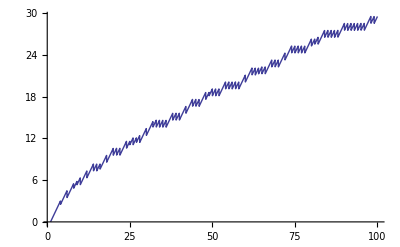

```mathematica
DiscretePlot[ divisorPrime[x], {x, 1, 100}]
```

```mathematica
divm[n_] := Sum[ (-1)^(k+1) d2[n, k] , {k, 1, 20 }]
```

```mathematica
Plot[ divm[x], {x, 1, 100}]
```